Definition of RK4

```mathematica
crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];
```

Compile the NDSolve parameter sweep

```mathematica
nonContInitMedium[t_]:=Piecewise[{
{Cos[4 Pi *t],-2≤t≤-1.5},
{t^2,-1.5 <t ≤-√2},
{Exp[t],-√2 <t ≤-1.101},
{0,-1.101 <t ≤-0.5},
{t+0.5,-0.5 <t }
}]
```

```mathematica
logistic2=Compile[
{{parameterList,_Real,1}},
Table[
sol=NDSolve[
{
x'[t] == x[t]*x[t-2]*(parameterList[[i]]- x[t-1]),
x[t/;t≤0] ==nonContInitMedium[t]
},
x[t],
{t,0,10},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},
StartingStepSize->0.001,
MaxSteps->10100
];
First@Evaluate[x[t]/.sol]/.t->10,
{i,1,Length[parameterList]}],
CompilationTarget->"C",
"RuntimeOptions"->"Speed"
]
```

CompiledFunction[…]

Run and Benchmark

```mathematica
nrOfParameters = 128;
parameterList =N@Range[0,2,2/(nrOfParameters-1)];
runtime=Timing[endvals=logistic2[parameterList]];
runtime[[1]]
```

40.25

Export endvals

```mathematica
SetDirectory[NotebookDirectory[]];
Export["logistic2_endvals.txt",data=Transpose[{parameterList,endvals}],"Table"]
```

logistic2_endvals.txt

Plot endvals

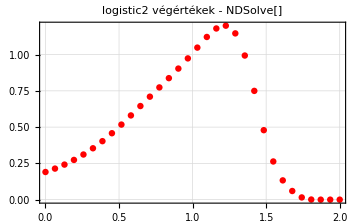

logistic2_endvals.png

```mathematica
plt=Show[
(*Plot[Evaluate[x[p][10]/.logistic1EndValues],{p,0,2},PlotStyle->Blue],*)
ListPlot[
data[[All,{1,2}]],
PlotStyle->Red,
FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"p","x(10)"},
PlotLabel->Style["logistic2 végértékek - NDSolve[]",Black,14]
]
]
Export["logistic2_endvals.png",plt,ImageResolution->1000]
```